# Generic ECE-3340 supplementary note: Polynomials

## 1. What is a polynomial

2x+1 ;  x is a variable. It is a polynomial of x.

5 q x^2 +c^2 -8; x and c are constant (can be unknown), q is a variable. Then it is a polynomial of q

x^2 y -2 (x+y^3) +7 is a polynomial of x and y if both are variables.

```mathematica
Plot3D[x^2 y -2 (x+y^3) +7 ,{x,-2,2},{y,-2,2}, PlotRange->All
,MeshFunctions->{#3&}, BoxRatios->{1,1,2}]
```

-Graphics3D-

## 2. For a single-variable polynomial, what are the most fundamental parameters

Consider:           4 x^4-28 x^3+69 x^2-97x+52
Are coefficients 4,        28,      69,      -97,      52 
the most fundamental parameters of the polynomial?

No. It is this:

```mathematica
Solve[4 x^4-28 x^3+69 x^2-97x+52==0,x]
```

```mathematica
{{x->1},{x->1-(3 ⅈ)/2},{x->1+(3 ⅈ)/2},{x->4}}
```

It is the zeros or roots that are fundamental to a polynomial. We construct a polynomial from the roots (up).

```mathematica
Expand[(x-1)(x-(1-(3 ⅈ)/2))(x-(1+(3 ⅈ)/2))  (x-4)]
```

13-(97 x)/4+(69 x^2)/4-7 x^3+x^4

We need just a proportional constant:

```mathematica
Expand[4*(x-1)(x-(1-(3 ⅈ)/2))(x-(1+(3 ⅈ)/2))  (x-4)]
```

52-97 x+69 x^2-28 x^3+4 x^4

Hence: 4 x^4-28 x^3+69 x^2-97x+52= 4 *(x-1)(x-(1-(3 ⅈ)/2))(x-(1+(3 ⅈ)/2))  (x-4)

For a real-coefficient polynomial, the fundamental way to express it is:
                     Q[s]=(s-z_1) (s-(z̄)_1) (s-z_2) (s-(z̄)_2) ... (s-z_n) (s-(z̄)_n)  (s-u_1) (s-u_2) ... 
where z_k,(z̄)_k  are a pair of conjugate roots, and u_1, u_2 are real roots.

## 3. Linear system transfer function

In this course, the reason we are interested in the polynomial is that it can be used to represent the Laplaced-transformed response or transfer function of a linear system.
(please review course materials of circuit analysis, signal analysis, or signals and systems)

What determines the behavior of these circuits or linear systems? The roots (or poles) of their Laplace transfer/response functions.

### 3.1 Example 1:

Please go to this website to watch the behavior of second-order circuits as functions of the Laplace TF poles.

http://courses.egr.uh.edu/ECE/ECE3340/Class%20 Notes2100/Lab_6/ECE2100_Lab6_v2 _p1.htm

Read additional notes about filters.

### 3.2 Example 2:

### 3.3 Example 3:

Discussion of PID controllers.

## 4. Example of coding for transfer functions

### 4.1 Usage of Product function

In general, a transfer function can be written as:
             P[s]/Q[s] = ((s-u_1) (s-u_2) ...)/((s-v_1) (s-v_2) ...)  =   (∏_(i=1)^p (s-u_i))/(∏_(j=1)^q (s-v_j))  
where u_i, i from 1 to p and v_j, j from 1 to q are the roots of the numerator and the denominator.

The mathematical symbol, ∏_(i=1)^p (s-u_i) is known as “product” and it can be used directly in Mathematica code:

```mathematica
u={1,3,2,-3,5,6};
∏_(i=1)^Length[u] (s-u[[i]])
```

(-6+s) (-5+s) (-3+s) (-2+s) (-1+s) (3+s)

To explicitly spell out the function without using the symbol, we can write:

```mathematica
Product[s-x,{x,u}]
```

(-6+s) (-5+s) (-3+s) (-2+s) (-1+s) (3+s)

Hence, suppose we have a list of roots, we can easily construct the TF programmatically. Below is an example.

### 4.2 Example 1

Suppose we have a list of desired {ω_n,η}, we first define function for the roots:

```mathematica
rootpairF[{ω_,η_}]:=ω {-η+ⅈ √(1-η^2),-η-ⅈ √(1-η^2)} ;
```

What if it is a single real root? then we just use the root directly. So let the list of single real roots and  {ω_n,η} be:

```mathematica
singleroot={a,b} ;
pairrootparm={{ω1,η1},{ω2,η2},{ω3,η3}};
```

What would be the polynomial? First, we get the root pairs:

```mathematica
rootpr=Table[rootpairF[u],{u,pairrootparm}]
```

{{(-η1+ⅈ √(1-η1^2)) ω1,(-η1-ⅈ √(1-η1^2)) ω1},{(-η2+ⅈ √(1-η2^2)) ω2,(-η2-ⅈ √(1-η2^2)) ω2},{(-η3+ⅈ √(1-η3^2)) ω3,(-η3-ⅈ √(1-η3^2)) ω3}}

```mathematica
Dimensions @ rootpr
```

{3,2}

The dimension above indicates that rootpr is a 3x2 array. But we want just a single list of 6. To do that, we need to flatten it by one level:

```mathematica
rootpr1=Flatten[rootpr,1]
```

{(-η1+ⅈ √(1-η1^2)) ω1,(-η1-ⅈ √(1-η1^2)) ω1,(-η2+ⅈ √(1-η2^2)) ω2,(-η2-ⅈ √(1-η2^2)) ω2,(-η3+ⅈ √(1-η3^2)) ω3,(-η3-ⅈ √(1-η3^2)) ω3}

```mathematica
Dimensions[rootpr1]
```

{6}

We see that it is just a list of 6 roots as expected. Now we are ready to construct the polynomial:

```mathematica
rootAll=Join[singleroot,rootpr1];
polyn=Product[s-u,{u,rootAll}]
```

(-a+s) (-b+s) (s-(-η1-ⅈ √(1-η1^2)) ω1) (s-(-η1+ⅈ √(1-η1^2)) ω1) (s-(-η2-ⅈ √(1-η2^2)) ω2) (s-(-η2+ⅈ √(1-η2^2)) ω2) (s-(-η3-ⅈ √(1-η3^2)) ω3) (s-(-η3+ⅈ √(1-η3^2)) ω3)

Let’s do a plot test:

```mathematica
{a,b}={-0.5,-1.2};
{{ω1,η1},{ω2,η2},{ω3,η3}}=Transpose[{{0.75,1.,2.2},{0.9,0.4,0.05}}]
```

{{0.75,0.9},{1.,0.4},{2.2,0.05}}

```mathematica
{xrange,yrange}={1.5*Max[Abs[Re[rootAll]]],1.2Max[Abs[Im[rootAll]]]}; (* the maximum x and y of all roots, multiple extra margin to set plot region *)
Plot3D[10.Log[10.,Abs[1/polyn/. s-> x+ⅈ y]]
,{x,-xrange,0.1xrange},{y,-yrange,yrange}
,ColorFunction->"BrightBands"
,MeshFunctions->{#3& ,Function @@ {{x,y,z}
,Arg[1/polyn /. s-> x+ⅈ y]} }
,MeshStyle-> {{Thickness[0.001],Orange},{Thickness[0.001],GrayLevel[0.75]}}
,PlotRange->{xrange{-1,0.1},yrange{-1,1},{-20,20}}
,PlotPoints->80, BoxRatios->{1.1 xrange,2 yrange,xrange}
,Background->Black, ImageSize->350]
```

-Graphics3D-

Notice that we define the polynomial with formulated roots, but not numeric values. Yet, as soon as we assign numeric values to the various root parameters, Mathematica will substitute numerical values into those symbols and we can plot the actual function.

```mathematica
{xrange,yrange}={1.5*Max[Abs[Re[rootAll]]],1.2Max[Abs[Im[rootAll]]]}; (* the maximum x and y of all roots, multiple extra margin to set plot region *)
Plot3D[10.Log[10.,Abs[(s+0.25)^3/polyn/. s-> x+ⅈ y]]
,{x,-xrange,0.1xrange},{y,-yrange,yrange}
,ColorFunction->"BrightBands"
,MeshFunctions->{#3& ,Function @@ {{x,y,z}
,Arg[(s+0.25)^3/polyn /. s-> x+ⅈ y]} }
,MeshStyle-> {{Thickness[0.001],Orange},{Thickness[0.001],GrayLevel[0.75]}}
,PlotRange->{xrange{-1,0.1},yrange{-1,1},{-20,20}}
,PlotPoints->80, BoxRatios->{1.1 xrange,2 yrange,1.5xrange}
,Background->Black, ImageSize->350]
```

-Graphics3D-

### 4.3 Example 3

This example is from HW3,
Let the lists of natural frequency and damping coefficient be:

```mathematica
ωL={ωn1,ωn2};ηL={ηa,ηb};
(* now we can create a list of all roots, we get a 2x2 table, each is another list of 2 roots *)
allroots=Table[rootpairF[{u,v}],{u,ωL},{v,ηL}]
```

{{{(-ηa+ⅈ √(1-ηa^2)) ωn1,(-ηa-ⅈ √(1-ηa^2)) ωn1},{(-ηb+ⅈ √(1-ηb^2)) ωn1,(-ηb-ⅈ √(1-ηb^2)) ωn1}},{{(-ηa+ⅈ √(1-ηa^2)) ωn2,(-ηa-ⅈ √(1-ηa^2)) ωn2},{(-ηb+ⅈ √(1-ηb^2)) ωn2,(-ηb-ⅈ √(1-ηb^2)) ωn2}}}

This is how you can see its structure:

```mathematica
Grid[allroots ,Frame-> All]
```

{(-ηa+ⅈ √(1-ηa^2)) ωn1,(-ηa-ⅈ √(1-ηa^2)) ωn1} | {(-ηb+ⅈ √(1-ηb^2)) ωn1,(-ηb-ⅈ √(1-ηb^2)) ωn1}
{(-ηa+ⅈ √(1-ηa^2)) ωn2,(-ηa-ⅈ √(1-ηa^2)) ωn2} | {(-ηb+ⅈ √(1-ηb^2)) ωn2,(-ηb-ⅈ √(1-ηb^2)) ωn2}

```mathematica
Dimensions[allroots]
```

{2,2,2}

We can define the top row, after flatten it as root1 and the second row is root2.

```mathematica
{root1,root2}={Flatten @ allroots[[1]],Flatten @ allroots[[2]]}
```

{{(-ηa+ⅈ √(1-ηa^2)) ωn1,(-ηa-ⅈ √(1-ηa^2)) ωn1,(-ηb+ⅈ √(1-ηb^2)) ωn1,(-ηb-ⅈ √(1-ηb^2)) ωn1},{(-ηa+ⅈ √(1-ηa^2)) ωn2,(-ηa-ⅈ √(1-ηa^2)) ωn2,(-ηb+ⅈ √(1-ηb^2)) ωn2,(-ηb-ⅈ √(1-ηb^2)) ωn2}}

```mathematica
Dimensions /@ {root1, root2}
```

{{4},{4}}

Now we can define the low-pass, hi-pass, and band-pass TF:

```mathematica
tflo=Product[ωn2/(s-u),{u,root2}  ] ;
tfhi=Product[s/(s-u),{u,root1 }] ;
tfbp=tfhi*tflo ;
```

We can put all into a function:

```mathematica
FilterTFdesign[{yr_,mon_,date_}]:=Block[{ωL,ηL,ωn1,ωn2
,ηa,ηb,allroots,roots,root1,root2,tfhi,tflo,tfbp}
, ClearAll[s]; (* s global is clear so that is Block has exclusive control *)
ωn1=1.+0.01 date;ωn2=ωn1 (1.2+0.2 Mod[yr,10]);
ηa=Cos[mon/25. π];ηb=Cos[Mod[mon+6,12]/25. π]; 
ωL={ωn1,ωn2};ηL={ηa,ηb};
allroots=Table[rootpairF[{u,v}],{u,ωL},{v,ηL}];
{root1,root2}={Flatten @ allroots[[1]],Flatten @ allroots[[2]]};
(* this is the output list of this function *)
{{root1,root2}  (* 1st element: a list of root1 and root2 *)
,tflo=Product[ωn2/(s-u),{u,root2}]  (* 2nd element *)
,tfhi=Product[s/(s-u),{u,root1}]  (* 3rd element *)
, tfbp=tfhi*tflo  (* 4th element *)
}
];
```

Example:

```mathematica
FilterTFdesign[{2008,10,12}]
```

{{{-0.346099+1.06518 ⅈ,-0.346099-1.06518 ⅈ,-0.981463+0.539564 ⅈ,-0.981463-0.539564 ⅈ},{-0.969077+2.98251 ⅈ,-0.969077-2.98251 ⅈ,-2.7481+1.51078 ⅈ,-2.7481-1.51078 ⅈ}},96.7173/(((0.969077-2.98251 ⅈ)+s) ((0.969077+2.98251 ⅈ)+s) ((2.7481-1.51078 ⅈ)+s) ((2.7481+1.51078 ⅈ)+s)),s^4/(((0.346099-1.06518 ⅈ)+s) ((0.346099+1.06518 ⅈ)+s) ((0.981463-0.539564 ⅈ)+s) ((0.981463+0.539564 ⅈ)+s)),(96.7173 s^4)/(((0.346099-1.06518 ⅈ)+s) ((0.346099+1.06518 ⅈ)+s) ((0.969077-2.98251 ⅈ)+s) ((0.969077+2.98251 ⅈ)+s) ((0.981463-0.539564 ⅈ)+s) ((0.981463+0.539564 ⅈ)+s) ((2.7481-1.51078 ⅈ)+s) ((2.7481+1.51078 ⅈ)+s))}

This is how to get the output: create variables to be used later:

```mathematica
{{rootHi,rootLo},tfloX,tfhiX,tfbpX}=FilterTFdesign[{2008,10,12}];
```

Some additional functions that can be used in the HW:

```mathematica
rootgraphF[rootLin_]:=Block[{polpts,root,maxr,rootlabel}
(* input a root list and it outputs a plot on polargrid *)
,root=Flatten[rootLin];

maxr=1.2 Max[Abs[root]];
polpts=Table[{Hue[(m-1.)/(Length[root]+1),1,1],Point[{Re[root[[m]]],Im[root[[m]]]}]},{m,Length[root]}];
rootlabel=Table[Text[Style[Subscript[z, m], 24,FontFamily->"Times New Roman"],1.15*{Re[root[[m]]],Im[root[[m]]]}],{m,Length[root]}];
Show[polargrid[1],Graphics[{PointSize[0.05],polpts,Yellow,rootlabel}]
,PlotRange-> {{-maxr,0.35},maxr{-1,1}}
,Background-> Black, ImageSize-> 300]
];
polargrid[g_]:=Graphics[{GrayLevel[g],Thickness[0.001],Arrowheads[0.07]
,Arrow[{{-1.4,0},{0.25,0}}]
,Arrow[{{0,-1.4},{0,1.4}}]
,Dashed,
Table[Circle[{0,0},r,{Pi/2,3 π/2}]
,{r,0.1,1.3,0.2}]
,Table[{Line[{{0,0},1.3{-j,√(1-j^2)}}]
,Line[{{0,0},1.3{-j,-√(1-j^2)}}]},{j,0.1,0.9,0.1}]}
];

TFgraphFunc[tfparmList_,var_]:=Block[{tfLoc,tf,rangex},
(* tfparmList={{tf1, plotrange1},
{tf2, plotrange2}
,...}
var is the symbol of the variable in the TF function *)

ClearAll[var];
If[ListQ[tfparmList] && Length[tfparmList]>0,tfLoc=tfparmList,tfLoc={tfparmList}];
If[Length[tfLoc]>0,
Table[{tf,rangex}=u;
{Plot3D[10.Log[10.,Abs[tf/. var-> x+ⅈ y]]  (* 1st element *)
,{x,-rangex,rangex},{y,-rangex,rangex}
,ColorFunction->"Rainbow"
,MeshFunctions->{#3& ,Function @@ {{x,y,z}
,Arg[tf /. var-> x+ⅈ y]} } 
,MeshStyle-> {{Thickness[0.001],Orange},{Thickness[0.001],GrayLevel[0.75]}}
,PlotPoints-> {50,50}, BoxRatios->{1,1,0.7}
,PlotRange->{rangex{-1,1},rangex{-1,1},{-20,20}}
,Background->Black, ImageSize->350]  

, LogLinearPlot[10Log[10.,Abs[(tf/.var-> ⅈ 2 π f)]]  (* 2nd element *)
,{f,0.001,100}
,PlotRange-> {{0.001,100},All},PlotStyle-> {Thickness[0.01],Hue[0.8,0.8,1]}
,Filling-> {1-> {Bottom,Hue[0.75,0.5,1,0.35]}}
,Frame-> True,GridLines-> Automatic,FrameStyle-> White,GridLinesStyle->GrayLevel[0.5]
,FrameLabel->(Style[#,18,FontFamily-> "Calibri"] &/@  
{"frequency (kHz)","amplitude (dB)"}) 
,Background->Black, ImageSize->350] 

,LogLinearPlot[Arg[(tf/.var-> ⅈ 2 π f)]/π             (* 3rd element *)
,{f,0.001,100}
,PlotRange-> {{0.001,100},{-1.1,1.1}}
,PlotStyle-> {Thickness[0.01],Hue[0.17,1,1]}
,Filling-> {1-> {0,Hue[0.15,1,1,0.4]}}
,Frame-> True,GridLines-> Automatic
,FrameStyle-> White,GridLinesStyle->GrayLevel[0.5]
,FrameLabel->(Style[#,18,FontFamily-> "Calibri"] &/@  
{"frequency (kHz)","phase (π)"}) 
,Background->Black, ImageSize->350] 
}
,{u,tfLoc}] (* 3 graphic elements for each TF of the input list  *)
,{}]
];
```

Here is a test of the various functions developed:

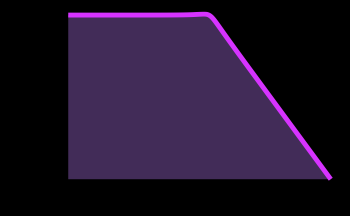
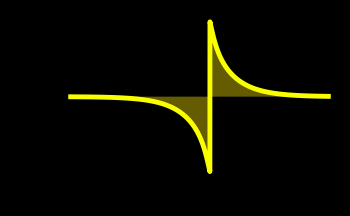
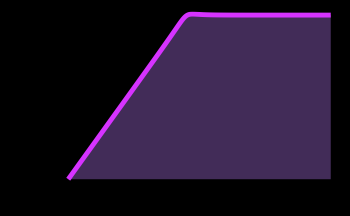
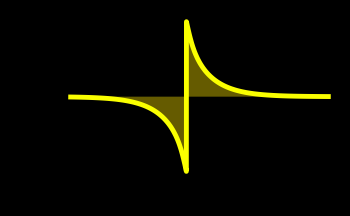
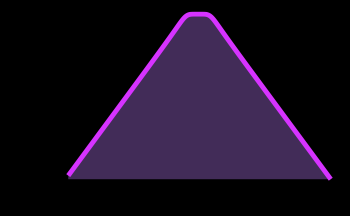
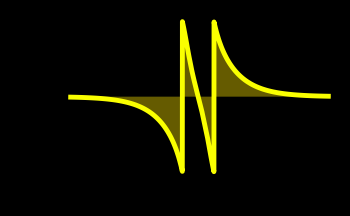
-Graphics3D- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics- | -Graphics-
-Graphics3D- | -Graphics- | -Graphics-

```mathematica
tfparmList= Transpose[{{tfloX,tfhiX,tfbpX}
,1.2*(Max /@{(Abs/@ rootLo),(Abs/@ rootHi),(Abs/@ rootLo)} )}];
TFgraphFunc[tfparmList,s] //Grid
```